### NHB paper Figure 4

Code that runs the simulation 50 times, each time incrementally increasing (and then decreasing) # of global connections, in order to explore hysteresis in the identity strengths

```mathematica
numRunsPerParam=50;
numLTimeSteps=1000;
iGlobMax=8;
(* need to run one sweep across n_glob and back at the time *)

For[iRun=1,iRun≤numRunsPerParam,iRun++,{

reInitialize[0];

tempAverIdStrengthsList={};
For[iGlob=0, iGlob≤iGlobMax, iGlob++,{
accStrengths=Array[0.0&,{nIdentity}];
changeConnections[iGlob];
simulate[numLTimeSteps,nGlobal,nLocal];
accStrengths+=calculateAvStrengths[pop];
AppendTo[tempAverIdStrengthsList,accStrengths];
}];

tempAverHysteresisList={accStrengths};
For[iGlob=iGlobMax-1, iGlob≥0, iGlob--,{
accStrengths=Array[0.0&,{nIdentity}];
changeConnections[iGlob];
simulate[numLTimeSteps,nGlobal,nLocal];
accStrengths+=calculateAvStrengths[pop];
PrependTo[tempAverHysteresisList,accStrengths];
}];

If[iRun==1,{
averIdStrengthsList=tempAverIdStrengthsList;
averHysteresisList=tempAverHysteresisList;
},{
averIdStrengthsList+=tempAverIdStrengthsList;
averHysteresisList+=tempAverHysteresisList;
}];

}];

averIdStrengthsList=averIdStrengthsList/numRunsPerParam;
averHysteresisList=averHysteresisList/numRunsPerParam;
```

Data from simulation used for graphs in Figure 4:

```mathematica
averIdStrengthsList
```

{{0.0500208,0.050088,0.050293,0.0509688},{0.0501391,0.0503944,0.0510935,0.254874},{0.0500396,0.0501551,0.0505582,0.95},{0.050329,0.0506898,0.0516748,0.95},{0.0512909,0.0524869,0.0545086,0.95},{0.0523981,0.0726019,0.685801,0.95},{0.107671,0.448229,0.95,0.95},{0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95}}

```mathematica
averHysteresisList
```

{{0.05,0.050002,0.0500398,0.948714},{0.0500025,0.0500246,0.0502086,0.95},{0.0500108,0.05004,0.838943,0.936333},{0.0500181,0.265593,0.940165,0.944469},{0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95}}

```mathematica
joinedList=Join[averIdStrengthsListᵀ ,averHysteresisListᵀ]ᵀ
```

{{0.0500208,0.050088,0.050293,0.0509688,0.05,0.050002,0.0500398,0.948714},{0.0501391,0.0503944,0.0510935,0.254874,0.0500025,0.0500246,0.0502086,0.95},{0.0500396,0.0501551,0.0505582,0.95,0.0500108,0.05004,0.838943,0.936333},{0.050329,0.0506898,0.0516748,0.95,0.0500181,0.265593,0.940165,0.944469},{0.0512909,0.0524869,0.0545086,0.95,0.95,0.95,0.95,0.95},{0.0523981,0.0726019,0.685801,0.95,0.95,0.95,0.95,0.95},{0.107671,0.448229,0.95,0.95,0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95},{0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95}}

```mathematica
joinedList={{0.050020772698972794,0.0500880450887003,0.05029298613092597,0.05096879572927,0.04999999999999998,0.05000200215799048,0.0500398405109361,0.9487135899226758},{0.05013906989873368,0.05039435851635586,0.05109348771741304,0.25487406021741055,0.05000246444355311,0.05002457034485282,0.05020860137491542,0.9500000000000006},{0.050039592593608566,0.05015507092992794,0.050558222611050335,0.9500000000000006,0.050010768489952,0.05003998906398771,0.8389428687351689,0.9363331950640054},{0.05032901424873766,0.05068977990091186,0.05167476881947696,0.9500000000000006,0.05001813258237887,0.2655925206507313,0.9401646893762693,0.9444685163375597},{0.05129088410937122,0.052486935406109894,0.054508648269599176,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.052398122452932724,0.07260186276183658,0.6858013064630571,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.10767136270465706,0.44822946000176617,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006},{0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006,0.9500000000000006}};
```

Aggregate version of the figure:

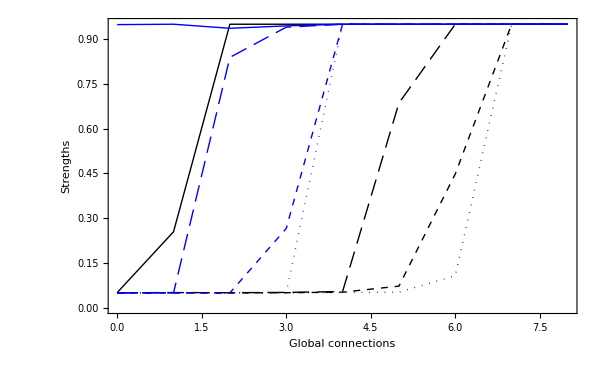

```mathematica
ListPlot[joinedListᵀ,Joined->True, Frame->True,PlotRange-> Full,PlotStyle->{{Dotted,Black},{Dashed,Black},{Dashing[{0.02,0.01}],Black},Black,{Dotted,Blue},{Dashed,Blue},{Dashing[{0.02,0.01}],Blue},Blue},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[14,FontFamily-> "Times"]]
```

Separate graphs for the strongest to the weakest identity. These four are combined in Figure 4 of the paper.

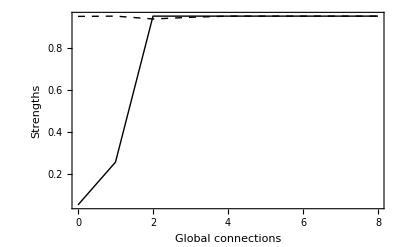

```mathematica
f1=ListPlot[{joinedListᵀ[[4]],joinedListᵀ[[8]]},Joined->True, Frame->True,PlotRange-> Full,
PlotStyle->{{Black},{Dashed,Black}},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[12,FontFamily-> "Times"]]
```

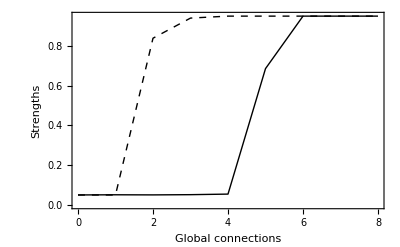

```mathematica
f2=ListPlot[{joinedListᵀ[[3]],joinedListᵀ[[7]]},Joined->True, Frame->True,PlotRange-> Full,
PlotStyle->{{Black},{Dashed,Black}},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[12,FontFamily-> "Times"]]
```

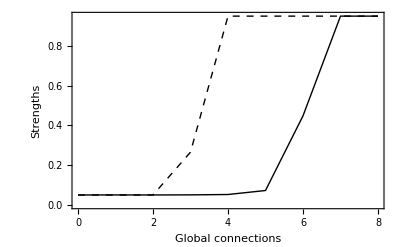

```mathematica
f3=ListPlot[{joinedListᵀ[[2]],joinedListᵀ[[6]]},Joined->True, Frame->True,PlotRange-> Full,
PlotStyle->{{Black},{Dashed,Black}},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[12,FontFamily-> "Times"]]
```

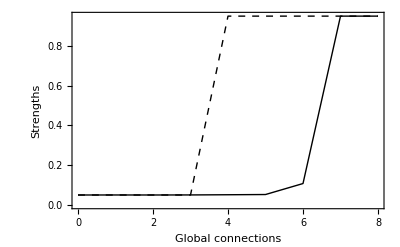

```mathematica
f4=ListPlot[{joinedListᵀ[[1]],joinedListᵀ[[5]]},Joined->True, Frame->True,PlotRange-> Full,PlotStyle->{{Black},{Dashed,Black}},DataRange->{0,8},FrameLabel->{"Global connections","Strengths"},LabelStyle->Directive[12,FontFamily-> "Times"]]
```

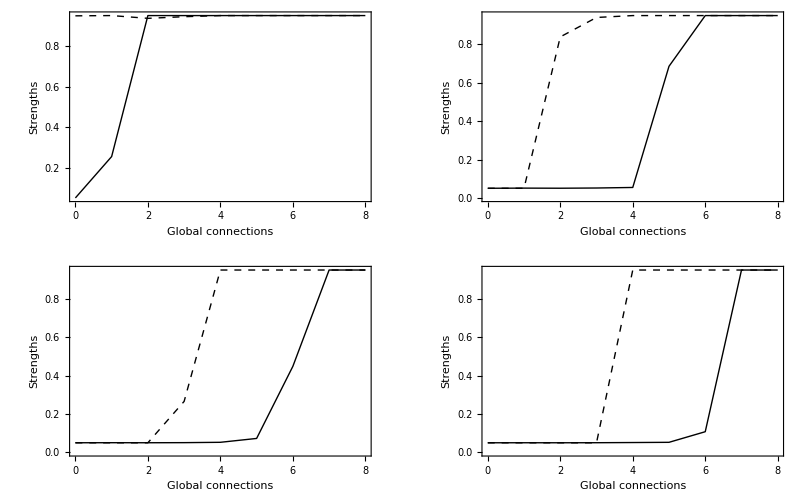

```mathematica
GraphicsGrid[{{f1,f2},{f3,f4}}]
```